# Project report

## Mathematica: Performance of Riffle/Partition vs Join/Transpose

D Malan

Department of Chemistry
University of Pretoria

14 March 2020

## Introduction

I’ve learned that it is important to check the performance of two different ways of doing something in arithmetic. (See my question at StackExchange Mathematica https://mathematica.stackexchange.com/questions/215823/why-the-difference-in-performance-array-vs-list-and-delete-vs-nothing.)

I have used two different ways of converting a list {t_1,t_2, t_3, ... } and a list {v_1,v_2, v_3, ... } to a list {{t_1, v_1}, {t_2,v_1}, {t_3,v_3}, ... }. I’ve often needed to do this to create lists of points for plotting in graphs.

## Experimental

### Preparation

```mathematica
n= 10;
a =Range[n];
b =Range[n+1, 2 n];
c=Range[2 n +1,3n];
```

### Riffle

Riffle joins two lists into a list with the items of the first list interleaved:

```mathematica
Riffle[a,b]
```

{1,11,2,12,3,13,4,14,5,15,6,16,7,17,8,18,9,19,10,20}

Partition can then split the list into a list of points suitable for plotting:

```mathematica
Partition[Riffle[a,b],2]
```

{{1,11},{2,12},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20}}

### Join/Transpose

Join will join two lists  into a single list with two items:

```mathematica
Join[{a}, {b}]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20}}

Transpose will then convert those lists into a list of points:

```mathematica
Transpose[Join[{a},{b}]]
```

{{1,11},{2,12},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20}}

## Calculations

### Preparation

Make lists with a large number of elements:

```mathematica
n= 1000000;
a =Range[n];
b =Range[n+1, 2 n];
c=Range[2 n +1,3n];
```

### Timing the calculations

Run a hundred trials of timing the two methods:

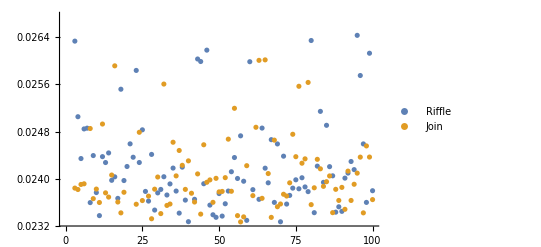

```mathematica
timing = {{"Riffle", "Join"}};
For[i=1, i <= 100, i++, 
AppendTo[
 timing
,{{AbsoluteTiming[Partition[Riffle[a,b],2]]//First,AbsoluteTiming[Partition[Riffle[a,b],2]]//First }}];
];
ListPlot[{timing[[2;;,1,1]], timing[[2;;,1,2]]}, PlotLegends-> timing[[1]]]
```

## Results

The results of the timing trials are shown in the figure above.

```mathematica
{timing[[1]],{Mean[timing[[2;;,1,1]]], Mean[timing[[2;;,1,2]]]}, {StandardDeviation[timing[[2;;,1,1]]], StandardDeviation[timing[[2;;,1,2]]]}}//TableForm
```

Riffle | Join
0.0244542 | 0.0244129
0.00147977 | 0.00141922

```mathematica
TTest[{timing[[2;;,1,1]], timing[[2;;,1,2]]},Automatic,{"TestStatisticTable", "TestStatistic", "TestConclusion"}]//TableForm
```

TTest::nortst: At least one of the p-values in {0,0}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

| Statistic
T | 0.201635
0.201635
The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the T test.

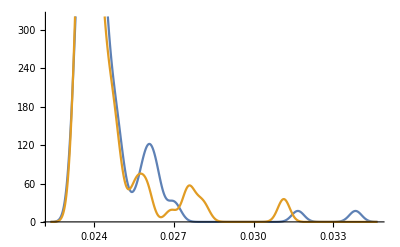

```mathematica
SmoothHistogram[{timing[[2;;,1,1]], timing[[2;;,1,2]]}]
```

## Discussion

Both methods are fast, but none is remarkable faster than the other.

The Join/Transpose method has the benefit that it can deal with more than two items with no modification. This might be required for preparing data for 3D plots, for example.

```mathematica
Transpose[Join[{a},{b}, {c}]]//Take[#, 5]&
```

{{1,1000001,2000001},{2,1000002,2000002},{3,1000003,2000003},{4,1000004,2000004},{5,1000005,2000005}}

## Conclusion

There is no difference between the Riffle and Join join methods as regards to performance, but the Join method is probably more general.

## Recommendations

Use the Join/Transpose method rather than the Riffle/Partition method.